#### Specifying an unbiased coinfection model

As discussed at some length in Alizon (2013), care must be taken to construct a coinfection model that is unbiased. In particular, in models where there are only four host classes (susceptible, infected with the resident strain, infected with the mutant strain, and coinfected), invading mutants have a frequency-dependent advantage over the resident strain because the mutant can infect both susceptible hosts and hosts infected with the resident strain, but because the mutant is assumed to be coming in at very low density, there is no offsetting advantage for the resident strain because it can only infect susceptible hosts. As the abundance of the mutant increases, this fitness advantage disappears. 

The simplest way to eliminate this fitness advantage is to allow double infections - that is, hosts infected with the resident strain can become “doubly-infected” by coming in contact with already-infected hosts. Although it is possible to allow hosts to become doubly-infected with the mutant strain as well, this will be exceedingly rare during invasion, and thus will have no impact on whether or not the mutant strain can invade or not.  

We make the following assumptions, with an eye towards making the model as general as possible:
(i) We let the parameter σ determine the susceptibility of singly infected hosts to double- or co-infection. For simplicity, we assume that this parameter is the same across all strain combinations. If σ = 0, then we revert to a model without coinfection.
(ii) We assume that the shedding rate from double infections is the same as that from single infections. This assumption is because we assume that shedding rate scales with the total abundance of parasites within a host, which depends on the host body size. Thus, a doubly infected host has the same total abundance of parasites and the same shedding rate.
(iii) We assume that in coinfected hosts, on the other hand, the strains compete: the total abundance of parasites is still determined by host size, but a fraction x of that total is the resident strain, with the remaining (1-x) being the mutant strain. Thus if x=1, coinfected hosts will shed only the resident strain, whereas if x=0.5, the two strains equally divide the total abundance. 
(iv) We also assume that the mutant strain sheds at a lower rate than the resident strains, c λ, where 0≤ c≤1.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x D1rm)-γ1 P1r;
dI1mdt=β1 S1 Pm-σ β1 I1m P1r-μ1 I1m;
dD1rmdt=σ β1 I1r Pm+σ β1 I1m P1r-μ1 D1rm;
dPmdt=c λ1 (I1m+(1-x) D1rm)-γ1 Pm;
```

Whether the mutant can invade can be determined by looking at the spectral radius of the next generation matrix:

```mathematica
Jac={{D[dS1dt,S1],D[dS1dt,I1r],D[dS1dt,D1rr],D[dS1dt,P1r],D[dS1dt,I1m],D[dS1dt,D1rm],D[dS1dt,Pm]},
{D[dI1dt,S1],D[dI1dt,I1r],D[dI1dt,D1rr],D[dI1dt,P1r],D[dI1dt,I1m],D[dI1dt,D1rm],D[dI1dt,Pm]},
{D[dD1rrdt,S1],D[dD1rrdt,I1r],D[dD1rrdt,D1rr],D[dD1rrdt,P1r],D[dD1rrdt,I1m],D[dD1rrdt,D1rm],D[dD1rrdt,Pm]},
{D[dP1rdt,S1],D[dP1rdt,I1r],D[dP1rdt,D1rr],D[dP1rdt,P1r],D[dP1rdt,I1m],D[dP1rdt,D1rm],D[dP1rdt,Pm]},
{D[dI1mdt,S1],D[dI1mdt,I1r],D[dI1mdt,D1rr],D[dI1mdt,P1r],D[dI1mdt,I1m],D[dI1mdt,D1rm],D[dI1mdt,Pm]},
{D[dD1rmdt,S1],D[dD1rmdt,I1r],D[dD1rmdt,D1rr],D[dD1rmdt,P1r],D[dD1rmdt,I1m],D[dD1rmdt,D1rm],D[dD1rmdt,Pm]},
{D[dPmdt,S1],D[dPmdt,I1r],D[dPmdt,D1rr],D[dPmdt,P1r],D[dPmdt,I1m],D[dPmdt,D1rm],D[dPmdt,Pm]}};
MatrixForm[Jmut=Jac[[5;;7,5;;7]]/.{I1m->0,D1rm->0,Pm->0}]
F={{0,0,β1 S1},{σ β1 P1r,0,σ β1 I1r},{0,0,0}};
V={{σ β1 P1r+μ1,0,0},{0,μ1,0},{-c λ1,-c λ1 (1-x),γ1}};
Jmut==F-V//Simplify
Inverse[V]
Eigenvalues[-V]
Dot[F,Inverse[V]]//MatrixForm
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

(-μ1-P1r β1 σ | 0 | S1 β1
P1r β1 σ | -μ1 | I1r β1 σ
c λ1 | c (1-x) λ1 | -γ1)

True

{{(γ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),0,0},{0,(γ1 μ1+P1r β1 γ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),0},{(c λ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ),(c (1-x) λ1 (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ),(μ1^2+P1r β1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ)}}

{-γ1,-μ1,-μ1-P1r β1 σ}

((c S1 β1 λ1 μ1)/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (c S1 (1-x) β1 λ1 (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (S1 β1 (μ1^2+P1r β1 μ1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ)
(P1r β1 γ1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ)+(c I1r β1 λ1 μ1 σ)/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (c I1r (1-x) β1 λ1 σ (μ1+P1r β1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ) | (I1r β1 σ (μ1^2+P1r β1 μ1 σ))/(γ1 μ1^2+P1r β1 γ1 μ1 σ)
0 | 0 | 0)

{0,-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2+√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2))),-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2-√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))}

The spectral radius must be larger than one for the mutant to be able to invade. The condition can be simplified somewhat:

```mathematica
-1/(2 γ1 μ1 (μ1+P1r β1 σ))β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2-√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))>1;
(-β1√(c λ1 (-4 P1r S1 (-1+x) γ1 μ1 σ (μ1+P1r β1 σ)+c λ1 (S1 μ1-I1r (-1+x) σ (μ1+P1r β1 σ))^2)))^2>(2 γ1 μ1 (σ P1r β1+μ1)+β1 (-c S1 λ1 μ1-c I1r λ1 μ1 σ+c I1r x λ1 μ1 σ-c I1r P1r β1 λ1 σ^2+c I1r P1r x β1 λ1 σ^2))^2//Simplify
```

γ1 μ1 (μ1+P1r β1 σ) (γ1 μ1 (μ1+P1r β1 σ)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))<0

Some further rearrangment leads to the following expression (which also must be greater than unity for the mutant to be able to invade):

```mathematica
γ1 μ1 (μ1+P1r β1 σ) (γ1 μ1 (μ1+P1r β1 σ)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))==γ1^2 μ1^2 (P1r β1 σ+μ1)^2-c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1))//Simplify
```

True

```mathematica
γ1 μ1 (P1r β1 σ+μ1) (γ1 μ1 (P1r β1 σ+μ1)+c β1 λ1 (I1r (-1+x) σ (μ1+P1r β1 σ)-S1 (μ1-P1r (-1+x) β1 σ)))<0;
γ1^2 μ1^2 (P1r β1 σ+μ1)^2-c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1))<0;
(c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1)))/(γ1^2 μ1^2 (P1r β1 σ+μ1)^2)>1;
```

Note that this expression is equivalent to the more biologically meaningful expression below. The first term is the probability that a spore in the environment encounters a host already infected with the resident strain. The second term is the expected amount of spores shed from a coinfected host. The third term is the probability a spore in the environment encounters a susceptible host. Once a host is singly infected with the mutant strain, there are two potential outcomes, captured by the terms in the parenthetical expression. The first term of the parenthetical is the probability that the singly infected host dies before becoming coinfected; the second term is the expected amount of shedding from a singly infected host. The third term of the parenthetical is the probability that the singly infected host will become coinfected; the fourth term is the expected amount of shedding from a coinfected host.

```mathematica
(c β1 λ1 γ1 μ1 (P1r β1 σ+μ1)  (S1 (P1r (1-x) σ β1+μ1)+I1r (1-x) σ (P1r β1 σ+μ1)))/(γ1^2 μ1^2 (P1r β1 σ+μ1)^2)==(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)//Simplify
```

True

The condition for invasion is that the spectral radius is greater than one, which can be simplified to the following equation, which depends on the equilibrium of the resident-only model. The equilibria of the resident-only model (in terms of the equilibrium abundance of parasites in the environment) are:

```mathematica
P1rEq=Solve[(dI1rdt/.Pm->0/.D1rm->0)==0,P1r]
D1rrEq=Solve[(dP1rdt/.P1rEq[[1]]/.D1rm->0)==0,D1rr]
S1Eq=Solve[(dD1rrdt/.D1rrEq[[1]]/.P1rEq[[1]])==0,S1]
```

{{P1r→(I1r μ1)/(β1 (S1-I1r σ))}}

{{D1rr→-(I1r S1 β1 λ1-I1r γ1 μ1-I1r^2 β1 λ1 σ)/(β1 λ1 (S1-I1r σ))}}

{{S1→(γ1 μ1)/(β1 λ1)}}

The spectral radius, evaluated at the equilbrium, is the following:

```mathematica
(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)/.P1rEq⟦1⟧/.S1Eq⟦1⟧//Simplify
```

(c (γ1 μ1+I1r (1-2 x) β1 λ1 σ))/(γ1 μ1)

Notice that if the resident and mutant are identical (x=0.5 and c=1) and coinfection is unbiased (σ=1), then the mutant is neutral (its fitness is equal to 1).

```mathematica
Simplify[(σ β1 I1r)/γ1 (c λ1 (1-x))/μ1+(β1 S1)/γ1 (μ1/(σ β1 P1r+μ1) (c λ1)/μ1+(σ β1 P1r)/(σ β1 P1r+μ1) (c λ1 (1-x))/μ1)/.P1rEq⟦1⟧/.S1Eq⟦1⟧/.c->1/.x->0.5/.σ->1]
```

1.

#### Specifying a two-host model with coinfection but without depletion of parasites from the environment

Now that I am confident in my ability to specify an unbiased coinfection model with a single host type, we can specify the coinfection model with two hosts and two specialist parasites, where the invading strain is a generalist.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -γ)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(γ μ1 μ2^2+P2r β2 γ μ1 μ2 σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(γ μ1^2 μ2+P1r β1 γ μ1 μ2 σ1)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(γ μ1),(c (1-x2) λ2)/(γ μ2),1/γ}}

{-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/(γ μ1) | (c S1 (1-x2) β1 λ2)/(γ μ2) | (S1 β1)/γ
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/(γ μ1) | (c S2 (1-x2) β2 λ2)/(γ μ2) | (S2 β2)/γ
(P1r β1 σ1 (γ μ1 μ2^2+P2r β2 γ μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/(γ μ1) | (c I1r (1-x2) β1 λ2 σ1)/(γ μ2) | (I1r β1 σ1)/γ
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (γ μ1^2 μ2+P1r β1 γ μ1 μ2 σ1) σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/(γ μ1) | (c I2r (1-x2) β2 λ2 σ2)/(γ μ2) | (I2r β2 σ2)/γ
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The invasion condition can be reexpressed as:

```mathematica
(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))>1;
(-√(c (-4 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))^2>((2 γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))-(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0

With some further manipulation, the invasion condition can be written as the following:

```mathematica
(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2-c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2)))<0;
(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2-c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2)))<0;
1/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2 (c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))>1;
```

While this condition is essentially impossible to interpret in its current form, it has a biologically meaningful form:

```mathematica
1/(γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))^2 (c γ μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)(S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2+P2r (1-x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (μ1+P1r (1-x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (1-x1) β1 λ1 μ2 σ1+I2r (1-x2) β2 λ2 μ1 σ2))))==(σ1 β1 I1r)/γ (c λ1 (1-x1))/μ1+(β1 S1)/γ (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/γ (c λ2 (1-x2))/μ2+(β2 S2)/γ (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2)//Simplify
Rm=(σ1 β1 I1r)/γ (c λ1 (1-x1))/μ1+(β1 S1)/γ (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/γ (c λ2 (1-x2))/μ2+(β2 S2)/γ (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
```

True

```mathematica
P1rEq=Solve[(dI1rdt/.Pm->0/.D1rm->0)==0,P1r]
D1rrEq=Solve[(dP1rdt/.P1rEq[[1]]/.D1rm->0)==0,D1rr]
S1Eq=Solve[(dD1rrdt/.D1rrEq[[1]]/.P1rEq[[1]])==0,S1]
P2rEq=Solve[(dI2rdt/.Pm->0/.D2rm->0)==0,P2r]
D2rrEq=Solve[(dP2rdt/.P2rEq[[1]]/.D2rm->0)==0,D2rr]
S2Eq=Solve[(dD2rrdt/.D2rrEq[[1]]/.P2rEq[[1]])==0,S2]
```

{{P1r→(I1r μ1)/(β1 (S1-I1r σ1))}}

{{D1rr→-(I1r S1 β1 λ1-I1r γ μ1-I1r^2 β1 λ1 σ1)/(β1 λ1 (S1-I1r σ1))}}

{{S1→(γ μ1)/(β1 λ1)}}

{{P2r→(I2r μ2)/(β2 (S2-I2r σ2))}}

{{D2rr→-(I2r S2 β2 λ2-I2r γ μ2-I2r^2 β2 λ2 σ2)/(β2 λ2 (S2-I2r σ2))}}

{{S2→(γ μ2)/(β2 λ2)}}

Note that if there is no cost of generalism, the generalist should have a R_m=2 (because the mutant’s invasion fitness is equal to the sum of its invasion fitnesses on each host separately).

```mathematica
Rm/.P1rEq⟦1⟧/.P2rEq⟦1⟧/.S1Eq⟦1⟧/.S2Eq⟦1⟧/.{c->1,x1->0.5,x2->0.5,σ1->1,σ2->1}//FullSimplify
```

2.

If you disallow coinfection, you recover the results from the single-infection model. Without depletion of parasites from the environment, everything is very simple, and the cost is all that matters.

```mathematica
Rm/.{σ1->0,σ2->0}
Rm/.{σ1->0,σ2->0}/.{S1->(γ μ1)/(β1 λ1),S2->(γ μ2)/(β2 λ2)}
```

(c S1 β1 λ1)/(γ μ1)+(c S2 β2 λ2)/(γ μ2)

2 c

What if you allow coinfection and the two strains are equal competitors? Interestingly, you get the same result. All that matters is the cost of generalism.

```mathematica
Simplify[Rm/.P1rEq⟦1⟧/.P2rEq⟦1⟧/.S1Eq⟦1⟧/.S2Eq⟦1⟧/.{x1->0.5,x2->0.5}]
```

2. c

#### Specifying a two-host model with coinfection with depletion of parasites from the environment

Now that I am confident in my ability to specify an unbiased coinfection model with a single host type, we can specify the coinfection model with two hosts and two specialist parasites, where the invading strain is a generalist.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 S1 P1r- β1 I1r P1r-β1 I1m P1r-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)-β2 S2 P2r- β2 I2r P2r- β2 I2m P2r-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-β1 S1 Pm-β2 S2 Pm-β1 I1r Pm-β2 I2r Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -I1r β1-S1 β1-I2r β2-S2 β2-γ)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1),(c (1-x2) λ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2),1/(I1r β1+S1 β1+I2r β2+S2 β2+γ)}}

{-I1r β1-S1 β1-I2r β2-S2 β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c S1 (1-x2) β1 λ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (S1 β1)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c S2 (1-x2) β2 λ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (S2 β2)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c I1r (1-x2) β1 λ2 σ1)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (I1r β1 σ1)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1) | (c I2r (1-x2) β2 λ2 σ2)/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ2) | (I2r β2 σ2)/(I1r β1+S1 β1+I2r β2+S2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The invasion condition can be reexpressed as:

```mathematica
(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))>1;
(-√(c (-4 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))^2>((2 (I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))-(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

(I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0

With some further manipulation, the invasion condition can be written as the following:

```mathematica
((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0;
-c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))>(I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2);
-1/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))>1;
```

While this condition is essentially impossible to interpret in its current form, it can be expressed in a more biologically meaningful way:

```mathematica
Rm=(σ1 β1 I1r)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(S1 β1+S2 β2+I1r β1+I2r β2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);
-1/((I1r β1+S1 β1+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))==Rm//Simplify
```

True

The invasion condition depends on the equilibria of the system when the generalist parasite is absent. These equilibria are found below.

```mathematica
Solve[(dI1rdt/.{Pm->0})==0,S1];
Solve[(dD1rrdt/.{Pm->0})==0,I1r];
D1rrEq2=Solve[(dP1rdt/.{D1rm->0,I1m->0}/.{S1->(I1r μ1+I1r P1r β1 σ1)/(P1r β1)}/.{I1r->(D1rr μ1)/(P1r β1 σ1)})==0,D1rr];
I1rEq2=Solve[(dD1rrdt/.{Pm->0})==0,I1r]/.{D1rr->(P1r^2 β1 γ σ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)};
S1Eq2=Simplify[Solve[(dI1rdt/.{Pm->0})==0,S1]/.{I1r->(P1r γ μ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}];
P1rEq2=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->(γ μ1 (μ1+P1r β1 σ1))/(β1 (λ1 (μ1+P1r β1 σ1)-μ1 (μ1+2 P1r β1 σ1)))}/.{I1r->(P1r γ μ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}/.{D1rr->(P1r^2 β1 γ σ1)/(λ1 μ1-μ1^2+P1r β1 λ1 σ1-2 P1r β1 μ1 σ1)}]==0,P1r];

Solve[(dI2rdt/.{Pm->0})==0,S2];
Solve[(dD2rrdt/.{Pm->0})==0,I2r];
D2rrEq2=Solve[(dP2rdt/.{D2rm->0,I2m->0}/.{S2->(I2r μ2+I2r P2r β2 σ2)/(P2r β2)}/.{I2r->(D2rr μ2)/(P2r β2 σ2)})==0,D2rr];
I2rEq2=Solve[(dD2rrdt/.{Pm->0})==0,I2r]/.{D2rr->(P2r^2 β2 γ σ2)/(λ2 μ2-μ2^2+P2r β2 λ2 σ2-2 P2r β2 μ2 σ2)};
S2Eq2=Simplify[Solve[(dI2rdt/.{Pm->0})==0,S2]/.{I2r->(P2r γ μ2)/(λ2 μ2-μ2^2+P2r β2 λ2 σ2-2 P2r β2 μ2 σ2)}];
P2rEq2=Solve[Simplify[dS2dt/.{D2rm->0,I2m->0,Pm->0}/.{S2->(γ μ2 (μ2+P2r β2 σ2))/(β2 (λ2 (μ2+P2r β2 σ2)-μ2 (μ2+2 P2r β2 σ2)))}/.{I2r->(P2r γ μ2)/(λ2 μ2-μ2^2+P2r β2 λ2 σ2-2 P2r β2 μ2 σ2)}/.{D2rr->(P2r^2 β2 γ σ2)/(λ2 μ2-μ2^2+P2r β2 λ2 σ2-2 P2r β2 μ2 σ2)}]==0,P2r];
```

Before going any further, it is useful to confirm that the equilibrium values found analytically agree with the equilibria found numerically (this was a problem previously). This requires specifying the allometric relationships underlying the host’s life history parameters and the parasites’ shedding rates. 

Allen et al. 2002 gives the allometric relationship between carrying capacity in individuals per km^2 and weight in grams, assuming that E = 0.78.
Savage et al. 2004 gives the allometric relationships between mortality rate (1/yr) and mass in grams, and between growth rate (1/yr) and weight in grams.
The growth rate data suggested a value of E=0.35, but Gillooly et al. 2001 suggested a value of E=0.43 for fish.

These differences are very non-trivial. For example, Allen et al. 2002 shows some data where log(K e^(-E/k T))=-20. If E=0.43, this value suggests a carrying capacity of 0.02 individuals/km^2, whereas a value of E=.78 yields 9800 individuals/km^2.

```mathematica
Solve[Log[K Exp[-Ε/(k T)]]==-20,K]/.{Ε->0.43,k->8.62/10^5,T->310}
Solve[Log[K Exp[-Ε/(k T)]]==-20,K]/.{Ε->0.78,k->8.62/10^5,T->310}
```

{{K→0.0200728}}

{{K→9793.09}}

Thus I will allow E to be different for the two functions.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
pars={β1->0.1,β2->0.1,γ->0.1,σ2->1,W->1000,T->270,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
sol=NDSolve[{S1'[t]==(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
I1r'[t]==(dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
D1rr'[t]==(dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
P1r'[t]==(dP1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
S1[0]==100,
I1r[0]==1,
D1rr[0]==1,
P1r[0]==1},{S1,I1r,D1rr,P1r},{t,0,1000}]
I1r[1000]/.sol
I1rEq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
S1[1000]/.sol
S1Eq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
D1rr[1000]/.sol
D1rrEq2/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol)
P1r[1000]/.sol
P1rEq2/.allom/.allompars/.pars
```

{{S1→InterpolatingFunction[{{0., 1000.}}, <>],I1r→InterpolatingFunction[{{0., 1000.}}, <>],D1rr→InterpolatingFunction[{{0., 1000.}}, <>],P1r→InterpolatingFunction[{{0., 1000.}}, <>]}}

{0.000894096}

{{I1r→{0.000894096}}}

{0.000894096}

{{S1→{0.000894096}}}

{6042.25}

{{D1rr→{6042.25}}}

{2.01757×10^7}

{{P1r→-2.98548},{P1r→2.01757×10^7-8.88178×10^-16 ⅈ},{P1r→-3.62722-1.30385×10^-8 ⅈ},{P1r→-2.37072+1.30385×10^-8 ⅈ}}

Now that we have confirmed that the analytical equilibria agree with the numerical simulation results, we can examine the invasion condition a bit more carefully. Focusing on the case where we fully allow coinfection (σ_1=σ_2=1) and where coinfecting strains equally divide host resources (x_1=x_2=1/2), the invasion condition can be expressed in terms of the equilibrium abundance of specialist parasites in the environment.

```mathematica
FullSimplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]/.D2rrEq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.{σ1->1,σ2->1,x1->1/2,x2->1/2}]
```

(c (-μ1 (μ2 (-2 λ1 λ2+λ2 μ1+λ1 μ2)+P2r β2 (-2 λ1 λ2+λ2 μ1+2 λ1 μ2))+P1r β1 (-μ2 (2 λ2 μ1+λ1 (-2 λ2+μ2))-2 P2r β2 (λ2 μ1+λ1 (-λ2+μ2)))))/(P2r β2 λ1 λ2 (P1r β1+μ1)+(P1r β1 (λ1 λ2-4 P2r β2 μ1)+μ1 (λ1 λ2-2 P2r β2 μ1)) μ2-μ1 (2 P1r β1+μ1) μ2^2)

Notice that if the numerator is smaller than the denominator before accounting for the cost of generalism (c), then the generalist will never be able to invade. This requires the following to be true: (β_1 P_(1r)(λ_1-2 μ_1)+(λ_1-μ_1) μ_1)(β_2 P_(2r)(λ_2-2 μ_2)+(λ_2-μ_2) μ_2)<0.

```mathematica
-μ1 (μ2 (-2 λ1 λ2+λ2 μ1+λ1 μ2)+P2r β2 (-2 λ1 λ2+λ2 μ1+2 λ1 μ2))+P1r β1 (-μ2 (2 λ2 μ1+λ1 (-2 λ2+μ2))-2 P2r β2 (λ2 μ1+λ1 (-λ2+μ2)))<P2r β2 λ1 λ2 (P1r β1+μ1)+(P1r β1 (λ1 λ2-4 P2r β2 μ1)+μ1 (λ1 λ2-2 P2r β2 μ1)) μ2-μ1 (2 P1r β1+μ1) μ2^2//Simplify
```

(P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1) (P2r β2 (λ2-2 μ2)+(λ2-μ2) μ2)<0

However, in order for the equilibrium abundances of susceptible hosts to be positive, it must be the case that β_1 P_(1r)(λ_1-2 μ_1)+(λ_1-μ_1) μ_1>0 and β_2 P_(2r)(λ_2-2 μ_2)+(λ_2-μ_2) μ_2>0. Thus it is the case that if c = 1, the generalist will always be able to invade.

```mathematica
S1Eq2/.σ1->1
λ1 (P1r β1+μ1)-μ1 (2 P1r β1+μ1)==P1r β1 (λ1-2 μ1)+(λ1-μ1) μ1//Simplify
S2Eq2/.σ2->1
λ2 (P2r β2+μ2)-μ2 (2 P2r β2+μ2)==P2r β2 (λ2-2 μ2)+(λ2-μ2) μ2//Simplify
```

{{S1→(γ μ1 (P1r β1+μ1))/(β1 (λ1 (P1r β1+μ1)-μ1 (2 P1r β1+μ1)))}}

True

{{S2→(γ μ2 (P2r β2+μ2))/(β2 (λ2 (P2r β2+μ2)-μ2 (2 P2r β2+μ2)))}}

True

The question at hand is how changing host traits like body size influences the magnitude of the generalist’s fitness. We can assess this by taking the derivative of R_m with respect to host body size.

```mathematica
dRmdW=Simplify[D[Simplify[Rm/.D1rrEq2[[1]]/.I1rEq2[[1]]/.S1Eq2[[1]]]/.D2rrEq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.{x1->1/2,x2->1/2,σ1->1,σ2->1}/.{λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],P2r->P2r[W]},W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W)}]
```

(c (β1^2 P1r[W]^2 (8 β2^2 P2r[W]^2 (λ1[W]^2 λ2[W] μ2[W]+4 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-8 λ2[W] μ2[W]+4 μ2[W]^2))+β2 P2r[W] μ2[W] (11 λ1[W]^2 λ2[W] μ2[W]+44 λ2[W] μ1[W]^2 μ2[W]+4 λ1[W] μ1[W] (4 λ2[W]^2-23 λ2[W] μ2[W]+8 μ2[W]^2))+4 μ2[W]^2 (λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+4 λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+2 λ1[W] μ1[W] (λ2[W]^2-4 λ2[W] μ2[W]+μ2[W]^2+2 W β2 λ2[W] P2r'[W])))+β1 P1r[W] μ1[W] (22 β2 P2r[W] μ2[W] (λ1[W]^2 λ2[W] μ2[W]+2 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (λ2[W]^2-6 λ2[W] μ2[W]+2 μ2[W]^2))+β2^2 P2r[W]^2 (16 λ1[W]^2 λ2[W] μ2[W]+32 λ2[W] μ1[W]^2 μ2[W]+λ1[W] μ1[W] (11 λ2[W]^2-92 λ2[W] μ2[W]+44 μ2[W]^2))+μ2[W]^2 (8 λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+16 λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+λ1[W] μ1[W] (11 λ2[W]^2-46 λ2[W] μ2[W]+11 μ2[W]^2+24 W β2 λ2[W] P2r'[W])))+μ1[W]^2 (4 β2^2 P2r[W]^2 (2 λ1[W]^2 λ2[W] μ2[W]+2 λ2[W] μ1[W]^2 μ2[W]+λ1[W] (λ2[W]^2 (μ1[W]-W β1 P1r'[W])+4 μ2[W]^2 (μ1[W]-W β1 P1r'[W])+4 λ2[W] μ2[W] (-2 μ1[W]+W β1 P1r'[W])))+β2 P2r[W] μ2[W] (11 λ1[W]^2 λ2[W] μ2[W]+11 λ2[W] μ1[W]^2 μ2[W]+2 λ1[W] (4 λ2[W]^2 (μ1[W]-W β1 P1r'[W])+8 μ2[W]^2 (μ1[W]-W β1 P1r'[W])+λ2[W] μ2[W] (-23 μ1[W]+12 W β1 P1r'[W])))+4 μ2[W]^2 (λ1[W]^2 λ2[W] (μ2[W]-W β2 P2r'[W])+λ2[W] μ1[W]^2 (μ2[W]-W β2 P2r'[W])+λ1[W] (λ2[W]^2 (μ1[W]-W β1 P1r'[W])+μ2[W]^2 (μ1[W]-W β1 P1r'[W])+2 λ2[W] (-2 μ1[W] μ2[W]+W β1 μ2[W] P1r'[W]+W β2 μ1[W] P2r'[W]))))))/(4 W (β1 P1r[W] (β2 P2r[W] (λ1[W] λ2[W]-4 μ1[W] μ2[W])+μ2[W] (λ1[W] λ2[W]-2 μ1[W] μ2[W]))+μ1[W] (β2 P2r[W] (λ1[W] λ2[W]-2 μ1[W] μ2[W])+μ2[W] (λ1[W] λ2[W]-μ1[W] μ2[W])))^2)

The denominator of (∂R_m)/(∂W)must be positive (because it involves a square), so we can focus our attention only on the numerator. After much simplification, the numerator can be rewritten in the expression below. The first term must be positive, implying that if increasing host body size decreases .08.08.08the equilibrium abundance of both specialist parasites in the environment (i.e., OverHat[P_(1r)]'(W)<0 and OverHat[P_(2r)'](W)<0), then increasing host body size is guaranteed to make it easier for the generalist parasite to invade (i.e., R_m'(W)>0).

```mathematica
Collect[Expand[Numerator[dRmdW]],{P1r'[W],P2r'[W]}]==c ( 4 λ2[W] μ2[W](2 β2^2 P2r[W]^2+μ2[W]^2)(β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 +4 λ1[W] μ1[W] (2 β1^2 P1r[W]^2+μ1[W]^2) (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2+11 (β2 P2r[W] λ2[W] μ2[W]^2(μ1[W](λ1[W]-μ1[W])+β1 P1r[W] (λ1[W]-2μ1[W]))^2+β1 P1r[W] λ1[W] μ1[W]^2(μ2[W](λ2[W]-μ2[W])+β2 P2r[W] (λ2[W]-2μ2[W]))^2))-4 c W β1 λ1[W] μ1[W]^2 (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2 P1r'[W]-4 c W β2 λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W]^2 P2r'[W]//Simplify
```

True

We can try to figure out the sign of OverHat[P_(1r)]'(W) and OverHat[P_(2r)]'(W) by implicit differentiation of the equilibrium conditions dS_1/dt=0 and dS_2/dt=0. Moreover, we can simplify those expressions a bit by taking advantage of the fact that, at equilibrium, the following must hold:

```mathematica
r1Eq=Solve[(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq2[[1]]/.I1rEq2[[1]]/.D1rrEq2[[1]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],K1->K1[W]}/.{σ1->1,σ1->1,x1->1/2,x2->1/2})==0,r1[W]]
r2Eq=Solve[(dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq2[[1]]/.I2rEq2[[1]]/.D2rrEq2[[1]]/.{r2->r2[W],λ2->λ2[W],μ2->μ2[W],P2r->P2r[W],K2->K2[W]}/.{σ1->1,σ2->1,x1->1/2,x2->1/2})==0,r2[W]]
```

{{r1[W]→(γ P1r[W] μ1[W] (β1 P1r[W]+μ1[W]))/((λ1[W] (β1 P1r[W]+μ1[W])-μ1[W] (2 β1 P1r[W]+μ1[W])) ((β1 γ P1r[W]^2)/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ P1r[W] μ1[W])/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ μ1[W] (β1 P1r[W]+μ1[W]))/(β1 (λ1[W] (β1 P1r[W]+μ1[W])-μ1[W] (2 β1 P1r[W]+μ1[W])))) (1-((β1 γ P1r[W]^2)/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ P1r[W] μ1[W])/(β1 P1r[W] λ1[W]-2 β1 P1r[W] μ1[W]+λ1[W] μ1[W]-μ1[W]^2)+(γ μ1[W] (β1 P1r[W]+μ1[W]))/(β1 (λ1[W] (β1 P1r[W]+μ1[W])-μ1[W] (2 β1 P1r[W]+μ1[W]))))/K1[W]))}}

{{r2[W]→(γ P2r[W] μ2[W] (β2 P2r[W]+μ2[W]))/((λ2[W] (β2 P2r[W]+μ2[W])-μ2[W] (2 β2 P2r[W]+μ2[W])) ((β2 γ P2r[W]^2)/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ P2r[W] μ2[W])/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ μ2[W] (β2 P2r[W]+μ2[W]))/(β2 (λ2[W] (β2 P2r[W]+μ2[W])-μ2[W] (2 β2 P2r[W]+μ2[W])))) (1-((β2 γ P2r[W]^2)/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ P2r[W] μ2[W])/(β2 P2r[W] λ2[W]-2 β2 P2r[W] μ2[W]+λ2[W] μ2[W]-μ2[W]^2)+(γ μ2[W] (β2 P2r[W]+μ2[W]))/(β2 (λ2[W] (β2 P2r[W]+μ2[W])-μ2[W] (2 β2 P2r[W]+μ2[W]))))/K2[W]))}}

Plugging these equilibrium values of r_1 and r_2 after implicit differentiation we can solve for OverHat[P_(1r)]'(W)  andOverHat[P_(2r)]'(W):

```mathematica
Simplify[Solve[(D[(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq2[[1]]/.I1rEq2[[1]]/.D1rrEq2[[1]]/.{r1->r1[W],λ1->λ1[W],λ2->λ2[W],μ1->μ1[W],μ2->μ2[W],P1r->P1r[W],K1->K1[W]}/.{σ1->1,σ1->1,x1->1/2,x2->1/2}),W]/.{μ1'[W]->(-μ1[W])/(4 W),λ1'[W]->(3 λ1[W])/(4 W),K1'[W]->(-3 K1[W])/(4 W),r1'[W]->(-r1[W])/(4 W)}/.r1Eq[[1]])==0,P1r'[W]]]
Simplify[Solve[(D[(dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq2[[1]]/.I2rEq2[[1]]/.D2rrEq2[[1]]/.{r2->r2[W],λ2->λ2[W],μ2->μ2[W],P2r->P2r[W],K2->K2[W]}/.{σ1->1,σ2->1,x1->1/2,x2->1/2}),W]/.{μ2'[W]->(-μ2[W])/(4 W),λ2'[W]->(3 λ2[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W),r2'[W]->(-r2[W])/(4 W)}/.r2Eq[[1]])==0,P2r'[W]]]
```

{{P1r'[W]→(P1r[W] μ1[W] (8 β1^4 γ P1r[W]^4+β1^3 γ P1r[W]^3 (2 λ1[W]+23 μ1[W])+μ1[W]^2 (-β1 K1[W] (λ1[W]-μ1[W])^2+2 γ μ1[W] (λ1[W]+μ1[W]))+β1^2 P1r[W]^2 (-β1 K1[W] (λ1[W]-2 μ1[W])^2+6 γ μ1[W] (λ1[W]+4 μ1[W]))+β1 P1r[W] μ1[W] (γ μ1[W] (6 λ1[W]+11 μ1[W])-2 β1 K1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2))))/(4 W (β1^4 γ P1r[W]^4 (λ1[W]-2 μ1[W])+2 β1^3 γ P1r[W]^3 (λ1[W]-μ1[W]) μ1[W]+2 β1 P1r[W] (λ1[W]-2 μ1[W]) μ1[W]^2 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+(λ1[W]-μ1[W]) μ1[W]^3 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+β1^2 P1r[W]^2 μ1[W] (β1 K1[W] (λ1[W]-2 μ1[W])^2+3 γ μ1[W]^2)))}}

{{P2r'[W]→(P2r[W] μ2[W] (8 β2^4 γ P2r[W]^4+β2^3 γ P2r[W]^3 (2 λ2[W]+23 μ2[W])+μ2[W]^2 (-β2 K2[W] (λ2[W]-μ2[W])^2+2 γ μ2[W] (λ2[W]+μ2[W]))+β2^2 P2r[W]^2 (-β2 K2[W] (λ2[W]-2 μ2[W])^2+6 γ μ2[W] (λ2[W]+4 μ2[W]))+β2 P2r[W] μ2[W] (γ μ2[W] (6 λ2[W]+11 μ2[W])-2 β2 K2[W] (λ2[W]^2-3 λ2[W] μ2[W]+2 μ2[W]^2))))/(4 W (β2^4 γ P2r[W]^4 (λ2[W]-2 μ2[W])+2 β2^3 γ P2r[W]^3 (λ2[W]-μ2[W]) μ2[W]+2 β2 P2r[W] (λ2[W]-2 μ2[W]) μ2[W]^2 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+(λ2[W]-μ2[W]) μ2[W]^3 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+β2^2 P2r[W]^2 μ2[W] (β2 K2[W] (λ2[W]-2 μ2[W])^2+3 γ μ2[W]^2)))}}

These expressions are more or less impossible to analyze. However, at least two lines of evidence suggest that OverHat[P_(1r)]'(W)  andOverHat[P_(2r)]'(W) are likely both positive, rather than negative. First, shedding rate is strongly positively correlated with host body size, implying that increasing host body mass should likely increase the abundance of parasites in the environment. Second, in the models without coinfection, increasing host body mass increased the abundance of parasites in the environment.

We can plug the expressions for OverHat[P_(1r)]'(W)  andOverHat[P_(2r)]'(W) into the expression for (∂R_m)/(∂W), but that expression is no easier to analyze.

```mathematica
c ( 4 λ2[W] μ2[W](2 β2^2 P2r[W]^2+μ2[W]^2)(β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 +4 λ1[W] μ1[W] (2 β1^2 P1r[W]^2+μ1[W]^2) (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2+11 (β2 P2r[W] λ2[W] μ2[W]^2(μ1[W](λ1[W]-μ1[W])+β1 P1r[W] (λ1[W]-2μ1[W]))^2+β1 P1r[W] λ1[W] μ1[W]^2(μ2[W](λ2[W]-μ2[W])+β2 P2r[W] (λ2[W]-2μ2[W]))^2))-4 c W β1 λ1[W] μ1[W]^2 (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2 P1r'[W]-4 c W β2 λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W]^2 P2r'[W]/.{P1r'[W]->(P1r[W] μ1[W] (8 β1^4 γ P1r[W]^4+β1^3 γ P1r[W]^3 (2 λ1[W]+23 μ1[W])+μ1[W]^2 (-β1 K1[W] (λ1[W]-μ1[W])^2+2 γ μ1[W] (λ1[W]+μ1[W]))+β1^2 P1r[W]^2 (-β1 K1[W] (λ1[W]-2 μ1[W])^2+6 γ μ1[W] (λ1[W]+4 μ1[W]))+β1 P1r[W] μ1[W] (γ μ1[W] (6 λ1[W]+11 μ1[W])-2 β1 K1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2))))/(4 W (β1^4 γ P1r[W]^4 (λ1[W]-2 μ1[W])+2 β1^3 γ P1r[W]^3 (λ1[W]-μ1[W]) μ1[W]+2 β1 P1r[W] (λ1[W]-2 μ1[W]) μ1[W]^2 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+(λ1[W]-μ1[W]) μ1[W]^3 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+β1^2 P1r[W]^2 μ1[W] (β1 K1[W] (λ1[W]-2 μ1[W])^2+3 γ μ1[W]^2)))}/.{P2r'[W]->(P2r[W] μ2[W] (8 β2^4 γ P2r[W]^4+β2^3 γ P2r[W]^3 (2 λ2[W]+23 μ2[W])+μ2[W]^2 (-β2 K2[W] (λ2[W]-μ2[W])^2+2 γ μ2[W] (λ2[W]+μ2[W]))+β2^2 P2r[W]^2 (-β2 K2[W] (λ2[W]-2 μ2[W])^2+6 γ μ2[W] (λ2[W]+4 μ2[W]))+β2 P2r[W] μ2[W] (γ μ2[W] (6 λ2[W]+11 μ2[W])-2 β2 K2[W] (λ2[W]^2-3 λ2[W] μ2[W]+2 μ2[W]^2))))/(4 W (β2^4 γ P2r[W]^4 (λ2[W]-2 μ2[W])+2 β2^3 γ P2r[W]^3 (λ2[W]-μ2[W]) μ2[W]+2 β2 P2r[W] (λ2[W]-2 μ2[W]) μ2[W]^2 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+(λ2[W]-μ2[W]) μ2[W]^3 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+β2^2 P2r[W]^2 μ2[W] (β2 K2[W] (λ2[W]-2 μ2[W])^2+3 γ μ2[W]^2)))}//Simplify
```

c (4 λ1[W] μ1[W] (2 β1^2 P1r[W]^2+μ1[W]^2) (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2-(β1 P1r[W] λ1[W] μ1[W]^3 (8 β1^4 γ P1r[W]^4+β1^3 γ P1r[W]^3 (2 λ1[W]+23 μ1[W])+μ1[W]^2 (-β1 K1[W] (λ1[W]-μ1[W])^2+2 γ μ1[W] (λ1[W]+μ1[W]))+β1^2 P1r[W]^2 (-β1 K1[W] (λ1[W]-2 μ1[W])^2+6 γ μ1[W] (λ1[W]+4 μ1[W]))+β1 P1r[W] μ1[W] (γ μ1[W] (6 λ1[W]+11 μ1[W])-2 β1 K1[W] (λ1[W]^2-3 λ1[W] μ1[W]+2 μ1[W]^2))) (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2)/(β1^4 γ P1r[W]^4 (λ1[W]-2 μ1[W])+2 β1^3 γ P1r[W]^3 (λ1[W]-μ1[W]) μ1[W]+2 β1 P1r[W] (λ1[W]-2 μ1[W]) μ1[W]^2 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+(λ1[W]-μ1[W]) μ1[W]^3 (β1 K1[W] (λ1[W]-μ1[W])-γ μ1[W])+β1^2 P1r[W]^2 μ1[W] (β1 K1[W] (λ1[W]-2 μ1[W])^2+3 γ μ1[W]^2))+4 λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W] (2 β2^2 P2r[W]^2+μ2[W]^2)+11 (β2 P2r[W] λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W]^2+β1 P1r[W] λ1[W] μ1[W]^2 (β2 P2r[W] (λ2[W]-2 μ2[W])+(λ2[W]-μ2[W]) μ2[W])^2)-(β2 P2r[W] λ2[W] (β1 P1r[W] (λ1[W]-2 μ1[W])+(λ1[W]-μ1[W]) μ1[W])^2 μ2[W]^3 (8 β2^4 γ P2r[W]^4+β2^3 γ P2r[W]^3 (2 λ2[W]+23 μ2[W])+μ2[W]^2 (-β2 K2[W] (λ2[W]-μ2[W])^2+2 γ μ2[W] (λ2[W]+μ2[W]))+β2^2 P2r[W]^2 (-β2 K2[W] (λ2[W]-2 μ2[W])^2+6 γ μ2[W] (λ2[W]+4 μ2[W]))+β2 P2r[W] μ2[W] (γ μ2[W] (6 λ2[W]+11 μ2[W])-2 β2 K2[W] (λ2[W]^2-3 λ2[W] μ2[W]+2 μ2[W]^2))))/(β2^4 γ P2r[W]^4 (λ2[W]-2 μ2[W])+2 β2^3 γ P2r[W]^3 (λ2[W]-μ2[W]) μ2[W]+2 β2 P2r[W] (λ2[W]-2 μ2[W]) μ2[W]^2 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+(λ2[W]-μ2[W]) μ2[W]^3 (β2 K2[W] (λ2[W]-μ2[W])-γ μ2[W])+β2^2 P2r[W]^2 μ2[W] (β2 K2[W] (λ2[W]-2 μ2[W])^2+3 γ μ2[W]^2)))

Because the above analytical approach failed to be tractable, we must resort to numerical simulation.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
```

```mathematica
RmAcrossWB=Table[Table[(c I1r (1-x1) β1 λ1 σ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2))+(S1 β1 ((c λ1)/(μ1+P1r β1 σ1)+(c P1r (1-x1) β1 λ1 σ1)/(μ1 (μ1+P1r β1 σ1))))/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)+(c I2r (1-x2) β2 λ2 σ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2))+(S2 β2 ((c λ2)/(μ2+P2r β2 σ2)+(c P2r (1-x2) β2 λ2 σ2)/(μ2 (μ2+P2r β2 σ2))))/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)/.I1rEq2[[1]]/.S1Eq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.P2rEq2[[2]]/.P1rEq2[[2]]/.allom/.allompars/.{β1->B,β2->B,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->270},{Wval,10,1000,10}],{B,0.01,1.01,0.05}];
```

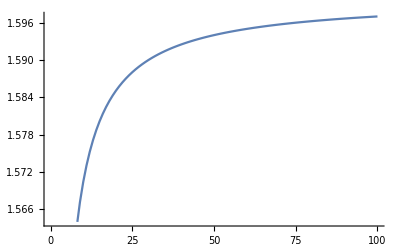

```mathematica
ListLinePlot[Re[RmAcrossWB[[20]]]]
```

```mathematica
RmAcrossWT=Table[Table[(c I1r (1-x1) β1 λ1 σ1)/(μ1 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2))+(S1 β1 ((c λ1)/(μ1+P1r β1 σ1)+(c P1r (1-x1) β1 λ1 σ1)/(μ1 (μ1+P1r β1 σ1))))/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)+(c I2r (1-x2) β2 λ2 σ2)/(μ2 (S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2))+(S2 β2 ((c λ2)/(μ2+P2r β2 σ2)+(c P2r (1-x2) β2 λ2 σ2)/(μ2 (μ2+P2r β2 σ2))))/(S1 β1+S2 β2+γ+I1r β1 σ1+I2r β2 σ2)/.I1rEq2[[1]]/.S1Eq2[[1]]/.I2rEq2[[1]]/.S2Eq2[[1]]/.P2rEq2[[2]]/.P1rEq2[[2]]/.allom/.allompars/.{β1->0.1,β2->0.1,γ->0.1,σ2->1,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2,W->Wval,T->Tval},{Wval,10,1010,100}],{Tval,270,310,5}];
```

Temperature has no effect.

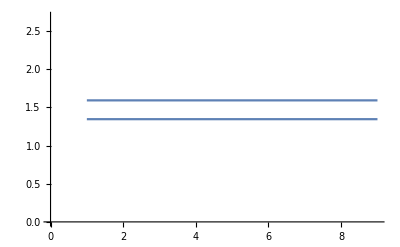

```mathematica
P1=ListLinePlot[Round[Re[RmAcrossWT[[;;,1]]],0.0001]];
P2=ListLinePlot[Round[Re[RmAcrossWT[[;;,5]]],0.0001]];
Show[P1,P2]
```

#### Specifying a two-host model with coinfection with depletion of parasites from the environment

What if the parasite attempts to infect all hosts, with no avoidance of double-infected hosts? This is probably the more biologically realistic scenario.

```mathematica
dS1dt=r1 (S1+I1r+D1rr+I1m+D1rm) (1-(S1+I1r+D1rr+I1m+D1rm)/K1)-β1 S1 (P1r+Pm);
dI1rdt=β1 S1 P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 (I1r+D1rr+x1 D1rm)-β1 (S1+I1r+D1rr+I1m) P1r-γ P1r;
dS2dt=r2 (S2+I2r+D2rr+I2m+D2rm) (1-(S2+I2r+D2rr+I2m+D2rm)/K2)-β2 S2 (P2r+Pm);
dI2rdt=β2 S2 P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)- β2 (S2+I2r+D2rr+I2m) P2r-γ P2r;

dI1mdt=β1 S1 Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 S2 Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m+λ2 I2m+(1-x1) λ1 D1rm+(1-x2) λ2 D2rm)-β1 (S1+I1r+D1rr) Pm-β2 (S2+I2r+D2rr) Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | S1 β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | S2 β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c λ1 | c λ2 | c (1-x1) λ1 | c (1-x2) λ2 | -(D1rr+I1r+S1) β1-(D2rr+I2r+S2) β2-γ)

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c (1-x1) λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1),(c (1-x2) λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2),1/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)}}

{-(D1rr+I1r+S1) β1-(D2rr+I2r+S2) β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

((S1 β1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S1 β1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S1 (1-x1) β1 λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c S1 (1-x2) β1 λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (S1 β1)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(S2 β2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (S2 β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c S2 (1-x1) β2 λ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c S2 (1-x2) β2 λ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (S2 β2)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r (1-x1) β1 λ1 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c I1r (1-x2) β1 λ2 σ1)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (I1r β1 σ1)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
(I2r β2 σ2 (c λ1 μ1 μ2^2+c P2r β2 λ1 μ1 μ2 σ2))/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c λ2 μ1^2 μ2+c P1r β1 λ2 μ1 μ2 σ1) σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r (1-x1) β2 λ1 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ1) | (c I2r (1-x2) β2 λ2 σ2)/(((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ) μ2) | (I2r β2 σ2)/((D1rr+I1r+S1) β1+(D2rr+I2r+S2) β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (-4 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (-4 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))/(2 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))}

The mutant can invade if the spectral radius is greater than one. The invasion condition can be reexpressed as:

```mathematica
(-√(c (-4 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) (P2r S2 (-1+x2) β2^2 λ2 μ1^2 σ2+P1r β1 σ1 (P2r S2 (-1+x2) β2^2 λ2 μ1 σ2+S1 (-1+x1) β1 λ1 μ2 (μ2+P2r β2 σ2)))+c (S2 β2 λ2 μ1 μ2 (μ1+P1r β1 σ1)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ1 μ2-(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))^2)))^2>((2 (D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))-(c S2 β2 λ2 μ1^2 μ2+c S1 β1 λ1 μ1 μ2^2+c P1r S2 β1 β2 λ2 μ1 μ2 σ1+c I1r β1 λ1 μ1 μ2^2 σ1-c I1r x1 β1 λ1 μ1 μ2^2 σ1+c I1r P1r β1^2 λ1 μ2^2 σ1^2-c I1r P1r x1 β1^2 λ1 μ2^2 σ1^2+c P2r S1 β1 β2 λ1 μ1 μ2 σ2+c I2r β2 λ2 μ1^2 μ2 σ2-c I2r x2 β2 λ2 μ1^2 μ2 σ2+c I1r P2r β1 β2 λ1 μ1 μ2 σ1 σ2-c I1r P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2+c I2r P1r β1 β2 λ2 μ1 μ2 σ1 σ2-c I2r P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2+c I1r P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2-c I1r P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2+c I2r P2r β2^2 λ2 μ1^2 σ2^2-c I2r P2r x2 β2^2 λ2 μ1^2 σ2^2+c I2r P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2-c I2r P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0

With some further manipulation, the invasion condition can be written as the following:

```mathematica
((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2))))<0;
-1/((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))>1;
```

True

While this condition is essentially impossible to interpret in its current form, it has a biologically meaningful form:

```mathematica
Rm=(σ1 β1 I1r)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (c λ1 (1-x1))/μ1+(β1 S1)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1))/μ1)+(σ2 β2 I2r)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (c λ2 (1-x2))/μ2+(β2 S2)/(D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2))/μ2);-1/((D1rr β1+I1r β1+S1 β1+D2rr β2+I2r β2+S2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))c (-S2 β2 λ2 μ1 (μ1+P1r β1 σ1) (μ2-P2r (-1+x2) β2 σ2)+(μ2+P2r β2 σ2) (S1 β1 λ1 μ2 (-μ1+P1r (-1+x1) β1 σ1)+(μ1+P1r β1 σ1) (I1r (-1+x1) β1 λ1 μ2 σ1+I2r (-1+x2) β2 λ2 μ1 σ2)))==Rm//Simplify
```

True

The relevant equilibria (for the two specialist parasites found without the generalist) are found below.

```mathematica
S1Eq=Solve[(dI1rdt/.{Pm->0})==0,S1];
I1rEq=Solve[(dD1rrdt/.{Pm->0})==0,I1r];
D1rrEq=Solve[(dP1rdt/.{D1rm->0,I1m->0}/.S1Eq[[1]]/.I1rEq[[1]])==0,D1rr]
I1rEq=Simplify[I1rEq/.D1rrEq[[1]]]
S1Eq=Simplify[S1Eq/.I1rEq[[1]]]
P1rEq=Solve[Simplify[dS1dt/.{D1rm->0,I1m->0,Pm->0}/.S1Eq[[1]]/.I1rEq[[1]]/.D1rrEq[[1]]]==0,P1r]

S2Eq=Solve[(dI2rdt/.{Pm->0})==0,S2];
I2rEq=Solve[(dD2rrdt/.{Pm->0})==0,I2r];
D2rrEq=Solve[(dP2rdt/.{D2rm->0,I2m->0}/.S2Eq[[1]]/.I2rEq[[1]])==0,D2rr]
I2rEq=Simplify[I2rEq/.D2rrEq[[1]]]
S2Eq=Simplify[S2Eq/.I2rEq[[1]]]
P2rEq=Solve[Simplify[dS2dt/.{D2rm->0,I2m->0,Pm->0}/.S2Eq[[1]]/.I2rEq[[1]]/.D2rrEq[[1]]]==0,P2r]
```

{{D1rr→-(P1r^2 β1 γ σ1)/((P1r β1-λ1+μ1) (μ1+P1r β1 σ1))}}

{{I1r→-(P1r γ μ1)/((P1r β1-λ1+μ1) (μ1+P1r β1 σ1))}}

{{S1→-(γ μ1)/(β1 (P1r β1-λ1+μ1))}}

{{P1r→(K1 r1 β1^2 λ1-2 K1 r1 β1^2 μ1-2 r1 β1 γ μ1-K1 β1^2 λ1 μ1+K1 β1^2 μ1^2-√K1 β1^(3/2) √(K1 r1^2 β1 λ1^2-2 K1 r1 β1 λ1^2 μ1+2 K1 r1 β1 λ1 μ1^2+4 r1 γ λ1 μ1^2+K1 β1 λ1^2 μ1^2-2 K1 β1 λ1 μ1^3+K1 β1 μ1^4))/(2 (K1 r1 β1^3+r1 β1^2 γ-K1 β1^3 μ1))},{P1r→(K1 r1 β1^2 λ1-2 K1 r1 β1^2 μ1-2 r1 β1 γ μ1-K1 β1^2 λ1 μ1+K1 β1^2 μ1^2+√K1 β1^(3/2) √(K1 r1^2 β1 λ1^2-2 K1 r1 β1 λ1^2 μ1+2 K1 r1 β1 λ1 μ1^2+4 r1 γ λ1 μ1^2+K1 β1 λ1^2 μ1^2-2 K1 β1 λ1 μ1^3+K1 β1 μ1^4))/(2 (K1 r1 β1^3+r1 β1^2 γ-K1 β1^3 μ1))}}

{{D2rr→-(P2r^2 β2 γ σ2)/((P2r β2-λ2+μ2) (μ2+P2r β2 σ2))}}

{{I2r→-(P2r γ μ2)/((P2r β2-λ2+μ2) (μ2+P2r β2 σ2))}}

{{S2→-(γ μ2)/(β2 (P2r β2-λ2+μ2))}}

{{P2r→(K2 r2 β2^2 λ2-2 K2 r2 β2^2 μ2-2 r2 β2 γ μ2-K2 β2^2 λ2 μ2+K2 β2^2 μ2^2-√K2 β2^(3/2) √(K2 r2^2 β2 λ2^2-2 K2 r2 β2 λ2^2 μ2+2 K2 r2 β2 λ2 μ2^2+4 r2 γ λ2 μ2^2+K2 β2 λ2^2 μ2^2-2 K2 β2 λ2 μ2^3+K2 β2 μ2^4))/(2 (K2 r2 β2^3+r2 β2^2 γ-K2 β2^3 μ2))},{P2r→(K2 r2 β2^2 λ2-2 K2 r2 β2^2 μ2-2 r2 β2 γ μ2-K2 β2^2 λ2 μ2+K2 β2^2 μ2^2+√K2 β2^(3/2) √(K2 r2^2 β2 λ2^2-2 K2 r2 β2 λ2^2 μ2+2 K2 r2 β2 λ2 μ2^2+4 r2 γ λ2 μ2^2+K2 β2 λ2^2 μ2^2-2 K2 β2 λ2 μ2^3+K2 β2 μ2^4))/(2 (K2 r2 β2^3+r2 β2^2 γ-K2 β2^3 μ2))}}

Before going any further, it is useful to confirm that the equilibrium values found analytically agree with the equilibria found numerically.

```mathematica
allom={K1->K0 Exp[0.78/(k T)] W^(-3/4),K2->K0 Exp[0.78/(k T)] (f W)^(-3/4),μ1->μ0 Exp[-0.43/(k T)] W^(-1/4),μ2->μ0 Exp[-0.43/(k T)] (f W)^(-1/4),λ1->λ0 Exp[-0.43/(k T)] W^(3/4),λ2->λ0 Exp[-0.43/(k T)] (f W)^(3/4),r1->r0 Exp[-0.43/(k T)] W^(-1/4),r2->r0 Exp[-0.43/(k T)] (f W)^(-1/4)};
allompars={k->8.617/10^5,K0->2.984/10^9,μ0->1.785 10^8,λ0->2 10^8,r0->2.21 10^10};
pars={β1->0.1,β2->0.1,γ->0.1,σ2->1,W->1000,T->300,σ1->1,f->0.9,c->0.8,x1->1/2,x2->1/2};
sol1=NDSolve[{S1'[t]==(dS1dt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
I1r'[t]==(dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
D1rr'[t]==(dD1rrdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
P1r'[t]==(dP1rdt/.{D1rm->0,I1m->0,Pm->0}/.{S1->S1[t],I1r->I1r[t],D1rr->D1rr[t],P1r->P1r[t]}/.allom/.allompars/.pars),
S1[0]==100,
I1r[0]==1,
D1rr[0]==1,
P1r[0]==1},{S1,I1r,D1rr,P1r},{t,0,1000}];
sol2=NDSolve[{S2'[t]==(dS2dt/.{D2rm->0,I2m->0,Pm->0}/.{S2->S2[t],I2r->I2r[t],D2rr->D2rr[t],P2r->P2r[t]}/.allom/.allompars/.pars),
I2r'[t]==(dI2rdt/.{D2rm->0,I2m->0,Pm->0}/.{S2->S2[t],I2r->I2r[t],D2rr->D2rr[t],P2r->P2r[t]}/.allom/.allompars/.pars),
D2rr'[t]==(dD2rrdt/.{D2rm->0,I2m->0,Pm->0}/.{S2->S2[t],I2r->I2r[t],D2rr->D2rr[t],P2r->P2r[t]}/.allom/.allompars/.pars),
P2r'[t]==(dP2rdt/.{D2rm->0,I2m->0,Pm->0}/.{S2->S2[t],I2r->I2r[t],D2rr->D2rr[t],P2r->P2r[t]}/.allom/.allompars/.pars),
S2[0]==100,
I2r[0]==1,
D2rr[0]==1,
P2r[0]==1},{S2,I2r,D2rr,P2r},{t,0,1000}];
P1r[1000]/.sol1
P2r[1000]/.sol2
P1rEq/.allom/.allompars/.pars
P2rEq/.allom/.allompars/.pars
RmSimp/.allom/.allompars/.pars/.P1r->(P1r[1000]/.sol1)/.P2r->(P2r[1000]/.sol2)
RmSimp/.P1rEq[[2]]/.P2rEq[[2]]/.allom/.allompars/.pars
```

{21116.9}

{19517.5}

{{P1r→-19.1073},{P1r→21116.9}}

{{P2r→-19.6173},{P2r→19517.5}}

{{0.801813}}

0.801813

Having verified that we have indeed found teh correct equilibria, we can plug those equilibria into the invasion condition, and derive a condition that depends only on the equilibrium abundances of resident parasites in the environment.

```mathematica
RmSimp=FullSimplify[Rm/.I1rEq[[1]]/.S1Eq[[1]]/.D1rrEq[[1]]/.I2rEq[[1]]/.S2Eq[[1]]/.D2rrEq[[1]]/.{σ2->1,σ1->1,x1->1/2,x2->1/2}]
```

(c (P2r β2 λ1+λ2 (P1r β1-2 λ1+μ1)+λ1 μ2))/(-λ1 λ2+(P1r β1+μ1) (P2r β2+μ2))

If the numerator is always less than the denominator, then the mutant can never invade, except possibly in the case where c=1. This requires the following inequality to hold:

```mathematica
P2r β2 λ1+λ2 (P1r β1-2 λ1+μ1)+λ1 μ2<-λ1 λ2+(P1r β1+μ1) (P2r β2+μ2)//Simplify
```

(P1r β1-λ1+μ1) (P2r β2-λ2+μ2)>0

If you look at the equilibrium values for S_1 and S_2, you see that β_1 P_(1r)-λ_1+μ_1<0 and β_2 P_(2r)-λ_2+μ_2<0. That forces the above inequality to be satisfied, implying that, when there is coinfection and doubly-infected hosts remove parasites from the environment without producing any parasites, the generalist will never be able to invade. That is an interesting and non-intuitive result.

```mathematica
S1Eq
S2Eq
```

{{S1→-(γ μ1)/(β1 (P1r β1-λ1+μ1))}}

{{S2→-(γ μ2)/(β2 (P2r β2-λ2+μ2))}}

#### Model with constant population size

```mathematica
dI1rdt=β1 (1-I1r-D1rr-I1m-D1rm) P1r-σ1 β1 I1r (P1r+Pm)-μ1 I1r;
dD1rrdt=σ1 β1 I1r P1r-μ1 D1rr;
dP1rdt=λ1 K1(I1r+D1rr+x1 D1rm)-β1 K1 P1r-γ P1r;

dI2rdt=β2 (1-I2r-D2rr-I2m-D2rm) P2r-σ2 β2 I2r (P2r+Pm)-μ2 I2r;
dD2rrdt=σ2 β2 I2r P2r-μ2 D2rr;
dP2rdt=λ2 (I2r+D2rr+x2 D2rm)K2-β2 K2 P2r-γ P2r;

dI1mdt=β1 (1-I1r-D1rr-I1m-D1rm) Pm-σ1 β1 I1m P1r-μ1 I1m;
dI2mdt=β2 (1-I2r-D2rr-I2m-D2rm) Pm-σ2 β2 I2m P2r-μ2 I2m;
dD1rmdt=σ1 β1 I1r Pm+σ1 β1 I1m P1r-μ1 D1rm;
dD2rmdt=σ2 β2 I2r Pm+σ2 β2 I2m P2r-μ2 D2rm;
dPmdt=c (λ1 I1m K1+λ2 I2m K2+(1-x1) λ1 D1rm K1+(1-x2) λ2 D2rm K2)-β1 K1 Pm-β2 K2 Pm-γ Pm;
```

Whether the mutant can invade will depend on the mutant Jacobian matrix:

```mathematica
MatrixForm[Jmut={{D[dI1mdt,I1m],D[dI1mdt,I2m],D[dI1mdt,D1rm],D[dI1mdt,D2rm],D[dI1mdt,Pm]},
{D[dI2mdt,I1m],D[dI2mdt,I2m],D[dI2mdt,D1rm],D[dI2mdt,D2rm],D[dI2mdt,Pm]},{D[dD1rmdt,I1m],D[dD1rmdt,I2m],D[dD1rmdt,D1rm],D[dD1rmdt,D2rm],D[dD1rmdt,Pm]},
{D[dD2rmdt,I1m],D[dD2rmdt,I2m],D[dD2rmdt,D1rm],D[dD2rmdt,D2rm],D[dD2rmdt,Pm]},
{D[dPmdt,I1m],D[dPmdt,I2m],D[dPmdt,D1rm],D[dPmdt,D2rm],D[dPmdt,Pm]}}/.{Pm->0,D1rm->0,I1m->0,I2m->0,D2rm->0}]
```

(-μ1-P1r β1 σ1 | 0 | 0 | 0 | (1-D1rr-I1r) β1
0 | -μ2-P2r β2 σ2 | 0 | 0 | (1-D2rr-I2r) β2
P1r β1 σ1 | 0 | -μ1 | 0 | I1r β1 σ1
0 | P2r β2 σ2 | 0 | -μ2 | I2r β2 σ2
c K1 λ1 | c K2 λ2 | c K1 (1-x1) λ1 | c K2 (1-x2) λ2 | -K1 β1-K2 β2-γ)

```mathematica
Solve[({dI1rdt==0,dD1rrdt==0,dP1rdt==0}/.{Pm->0,D1rm->0,I1m->0}),{I1r,D1rr,P1r}]//Simplify
Solve[({dI2rdt==0,dD2rrdt==0,dP2rdt==0}/.{Pm->0,D2rm->0,I2m->0}),{I2r,D2rr,P2r}]//Simplify
```

{{I1r→0,D1rr→0,P1r→0},{I1r→-((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),D1rr→((K1 β1 (λ1-μ1)-γ μ1)^2 σ1)/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1))),P1r→(K1 β1 (λ1-μ1)-γ μ1)/(β1 (K1 β1+γ))}}

{{I2r→0,D2rr→0,P2r→0},{I2r→-((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),D2rr→((K2 β2 (λ2-μ2)-γ μ2)^2 σ2)/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2))),P2r→(K2 β2 (λ2-μ2)-γ μ2)/(β2 (K2 β2+γ))}}

```mathematica
F={{0,0,0,0,Jmut[[1,5]]},
{0,0,0,0,Jmut[[2,5]]},
{Jmut[[3,1]],0,0,0,Jmut[[3,5]]},
{0,Jmut[[4,2]],0,0,Jmut[[4,5]]},
{0,0,0,0,0}};
V=F-Jmut;
(* Confirming that V meets the conditions to use the NGT *)
Inverse[V]
Eigenvalues[-V]
MatrixForm[Dot[F,Inverse[V]]]
Simplify[Eigenvalues[Dot[F,Inverse[V]]]]
```

{{(μ1 μ2^2+P2r β2 μ1 μ2 σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0,0},{0,(μ1^2 μ2+P1r β1 μ1 μ2 σ1)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),0,0,0},{0,0,1/μ1,0,0},{0,0,0,1/μ2,0},{(c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)),(c K1 (1-x1) λ1)/((K1 β1+K2 β2+γ) μ1),(c K2 (1-x2) λ2)/((K1 β1+K2 β2+γ) μ2),1/(K1 β1+K2 β2+γ)}}

{-K1 β1-K2 β2-γ,-μ1,-μ2,-μ1-P1r β1 σ1,-μ2-P2r β2 σ2}

(((1-D1rr-I1r) β1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D1rr-I1r) β1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D1rr-I1r) K1 (1-x1) β1 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D1rr-I1r) K2 (1-x2) β1 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D1rr-I1r) β1)/(K1 β1+K2 β2+γ)
((1-D2rr-I2r) β2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | ((1-D2rr-I2r) β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c (1-D2rr-I2r) K1 (1-x1) β2 λ1)/((K1 β1+K2 β2+γ) μ1) | (c (1-D2rr-I2r) K2 (1-x2) β2 λ2)/((K1 β1+K2 β2+γ) μ2) | ((1-D2rr-I2r) β2)/(K1 β1+K2 β2+γ)
(P1r β1 σ1 (μ1 μ2^2+P2r β2 μ1 μ2 σ2))/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I1r β1 σ1 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (I1r β1 σ1 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I1r K1 (1-x1) β1 λ1 σ1)/((K1 β1+K2 β2+γ) μ1) | (c I1r K2 (1-x2) β1 λ2 σ1)/((K1 β1+K2 β2+γ) μ2) | (I1r β1 σ1)/(K1 β1+K2 β2+γ)
(I2r β2 σ2 (c K1 λ1 μ1 μ2^2+c K1 P2r β2 λ1 μ1 μ2 σ2))/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (P2r β2 (μ1^2 μ2+P1r β1 μ1 μ2 σ1) σ2)/(μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(I2r β2 (c K2 λ2 μ1^2 μ2+c K2 P1r β1 λ2 μ1 μ2 σ1) σ2)/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)) | (c I2r K1 (1-x1) β2 λ1 σ2)/((K1 β1+K2 β2+γ) μ1) | (c I2r K2 (1-x2) β2 λ2 σ2)/((K1 β1+K2 β2+γ) μ2) | (I2r β2 σ2)/(K1 β1+K2 β2+γ)
0 | 0 | 0 | 0 | 0)

{0,0,0,-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))),-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2-√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)))}

```mathematica
-((-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2+√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))/(2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)))>1;
(√(c (4 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((-1+D2rr+I2r) K2 P2r (-1+x2) β2^2 λ2 μ1 (μ1+P1r β1 σ1) σ2+(-1+D1rr+I1r) K1 P1r (-1+x1) β1^2 λ1 μ2 σ1 (μ2+P2r β2 σ2))+c (K1 β1 λ1 μ2 (I1r P1r (-1+x1) β1 σ1^2+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (I2r P2r (-1+x2) β2 σ2^2+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))^2)))^2>((2 (K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))+(-c K2 β2 λ2 μ1^2 μ2+c D2rr K2 β2 λ2 μ1^2 μ2+c I2r K2 β2 λ2 μ1^2 μ2-c K1 β1 λ1 μ1 μ2^2+c D1rr K1 β1 λ1 μ1 μ2^2+c I1r K1 β1 λ1 μ1 μ2^2-c K2 P1r β1 β2 λ2 μ1 μ2 σ1+c D2rr K2 P1r β1 β2 λ2 μ1 μ2 σ1+c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1-c I1r K1 β1 λ1 μ1 μ2^2 σ1+c I1r K1 x1 β1 λ1 μ1 μ2^2 σ1-c I1r K1 P1r β1^2 λ1 μ2^2 σ1^2+c I1r K1 P1r x1 β1^2 λ1 μ2^2 σ1^2-c K1 P2r β1 β2 λ1 μ1 μ2 σ2+c D1rr K1 P2r β1 β2 λ1 μ1 μ2 σ2+c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ2-c I2r K2 β2 λ2 μ1^2 μ2 σ2+c I2r K2 x2 β2 λ2 μ1^2 μ2 σ2-c I1r K1 P2r β1 β2 λ1 μ1 μ2 σ1 σ2+c I1r K1 P2r x1 β1 β2 λ1 μ1 μ2 σ1 σ2-c I2r K2 P1r β1 β2 λ2 μ1 μ2 σ1 σ2+c I2r K2 P1r x2 β1 β2 λ2 μ1 μ2 σ1 σ2-c I1r K1 P1r P2r β1^2 β2 λ1 μ2 σ1^2 σ2+c I1r K1 P1r P2r x1 β1^2 β2 λ1 μ2 σ1^2 σ2-c I2r K2 P2r β2^2 λ2 μ1^2 σ2^2+c I2r K2 P2r x2 β2^2 λ2 μ1^2 σ2^2-c I2r K2 P1r P2r β1 β2^2 λ2 μ1 σ1 σ2^2+c I2r K2 P1r P2r x2 β1 β2^2 λ2 μ1 σ1 σ2^2))^2//Simplify
```

(K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2) ((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (K1 β1 λ1 μ2 (-P1r (-1+x1) β1 σ1 (-1+D1rr+I1r-I1r σ1)+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (-P2r (-1+x2) β2 σ2 (-1+D2rr+I2r-I2r σ2)+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2))))<0

```mathematica
((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2)+c (K1 β1 λ1 μ2 (-P1r (-1+x1) β1 σ1 (-1+D1rr+I1r-I1r σ1)+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (-P2r (-1+x2) β2 σ2 (-1+D2rr+I2r-I2r σ2)+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2))))<0;
1/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))(-c (K1 β1 λ1 μ2 (-P1r (-1+x1) β1 σ1 (-1+D1rr+I1r-I1r σ1)+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (-P2r (-1+x2) β2 σ2 (-1+D2rr+I2r-I2r σ2)+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))
)>1;
Rm=(σ1 β1 I1r)/(β1 K1+β2 K2+γ) (c λ1 (1-x1) K1)/μ1+(β1 (1-I1r-D1rr))/(β1 K1+β2 K2+γ) (μ1/(σ1 β1 P1r+μ1) (c λ1 K1)/μ1+(σ1 β1 P1r)/(σ1 β1 P1r+μ1) (c λ1 (1-x1) K1)/μ1)+(σ2 β2 I2r)/(β1 K1+β2 K2+γ) (c λ2 (1-x2) K2)/μ2+(β2 (1-I2r-D2rr))/(β1 K1+β2 K2+γ) (μ2/(σ2 β2 P2r+μ2) (c λ2 K2)/μ2+(σ2 β2 P2r)/(σ2 β2 P2r+μ2) (c λ2 (1-x2) K2)/μ2);
Rm==1/((K1 β1+K2 β2+γ) μ1 μ2 (μ1+P1r β1 σ1) (μ2+P2r β2 σ2))(-c (K1 β1 λ1 μ2 (-P1r (-1+x1) β1 σ1 (-1+D1rr+I1r-I1r σ1)+μ1 (-1+D1rr+I1r-I1r σ1+I1r x1 σ1)) (μ2+P2r β2 σ2)+K2 β2 λ2 μ1 (μ1+P1r β1 σ1) (-P2r (-1+x2) β2 σ2 (-1+D2rr+I2r-I2r σ2)+μ2 (-1+D2rr+I2r-I2r σ2+I2r x2 σ2)))
)//Simplify
```

True

Equilibria:

```mathematica
Solve[(dD1rrdt/.{Pm->0})==0,I1r]
Solve[(dP1rdt/.{D1rm->0}/.{I1r->(D1rr μ1)/(P1r β1 σ1)})==0,D1rr]
Solve[Simplify[dI1rdt/.{D1rm->0,I1m->0,Pm->0}/.{I1r->(D1rr μ1)/(P1r β1 σ1)}/.{D1rr->(P1r^2 β1 (K1 β1+γ) σ1)/(K1 λ1 (μ1+P1r β1 σ1))}]==0,P1r]
Simplify[Solve[(dP1rdt/.{D1rm->0}/.{I1r->(D1rr μ1)/(P1r β1 σ1)})==0,D1rr]/.{P1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(β1 (K1 β1+γ))}]
Simplify[Solve[(dD1rrdt/.{Pm->0})==0,I1r]/.{D1rr->(P1r^2 β1 (K1 β1+γ) σ1)/(K1 λ1 (μ1+P1r β1 σ1))}/.{P1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(β1 (K1 β1+γ))}]

Solve[(dD2rrdt/.{Pm->0})==0,I2r]
Solve[(dP2rdt/.{D2rm->0}/.{I2r->(D2rr μ2)/(P2r β2 σ2)})==0,D2rr]
Solve[Simplify[dI2rdt/.{D2rm->0,I2m->0,Pm->0}/.{I2r->(D2rr μ2)/(P2r β2 σ2)}/.{D2rr->(P2r^2 β2 (K2 β2+γ) σ2)/(K2 λ2 (μ2+P2r β2 σ2))}]==0,P2r]
Simplify[Solve[(dP2rdt/.{D2rm->0}/.{I2r->(D2rr μ2)/(P2r β2 σ2)})==0,D2rr]/.{P2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(β2 (K2 β2+γ))}]
Simplify[Solve[(dD2rrdt/.{Pm->0})==0,I2r]/.{D2rr->(P2r^2 β2 (K2 β2+γ) σ2)/(K2 λ2 (μ2+P2r β2 σ2))}/.{P2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(β2 (K2 β2+γ))}]
```

{{I1r→(D1rr μ1)/(P1r β1 σ1)}}

{{D1rr→(P1r^2 β1 (K1 β1+γ) σ1)/(K1 λ1 (μ1+P1r β1 σ1))}}

{{P1r→0},{P1r→(K1 β1 λ1-K1 β1 μ1-γ μ1)/(β1 (K1 β1+γ))}}

{{D1rr→((K1 β1 (λ1-μ1)-γ μ1)^2 σ1)/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1)))}}

{{I1r→-((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1)))}}

{{I2r→(D2rr μ2)/(P2r β2 σ2)}}

{{D2rr→(P2r^2 β2 (K2 β2+γ) σ2)/(K2 λ2 (μ2+P2r β2 σ2))}}

{{P2r→0},{P2r→(K2 β2 λ2-K2 β2 μ2-γ μ2)/(β2 (K2 β2+γ))}}

{{D2rr→((K2 β2 (λ2-μ2)-γ μ2)^2 σ2)/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2)))}}

{{I2r→-((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2)))}}

We can simplify this expression considerably, to c (1+γ/(β_1 K_1+β_2 K_2+γ)):

```mathematica
Simplify[Rm/.{I1r->-((K1 β1+γ) μ1 (γ μ1+K1 β1 (-λ1+μ1)))/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1)))}/.{P1r->(K1 β1 λ1-K1 β1 μ1-γ μ1)/(β1 (K1 β1+γ))}/.{D1rr->((K1 β1 (λ1-μ1)-γ μ1)^2 σ1)/(K1 β1 λ1 (-γ μ1 (-1+σ1)+K1 β1 (μ1+λ1 σ1-μ1 σ1)))}/.{P2r->(K2 β2 λ2-K2 β2 μ2-γ μ2)/(β2 (K2 β2+γ))}/.{D2rr->((K2 β2 (λ2-μ2)-γ μ2)^2 σ2)/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2)))}/.{I2r->-((K2 β2+γ) μ2 (γ μ2+K2 β2 (-λ2+μ2)))/(K2 β2 λ2 (-γ μ2 (-1+σ2)+K2 β2 (μ2+λ2 σ2-μ2 σ2)))}/.{σ1->1,σ2->1,x1->1/2,x2->1/2}]==c(1+γ/(K1 β1+K2 β2+γ))//Simplify
```

True

Increasing body mass will increase R_m because it decreases the abundance of each host, thereby making it more likely that a parasite “washes out” of the environment without infecting either host. Thereby, generalism benefits the parasite because it increases the total number of hosts available to it. Increasing temperature has a similar affect.

```mathematica
D[c(1+γ/(K1 β1+K2 β2+γ))/.{K1->K1[W],K2->K2[W]},W]/.{K1'[W]->(-3 K1[W])/(4 W),K2'[W]->(-3 K2[W])/(4 W)}//Simplify
D[c(1+γ/(K1 β1+K2 β2+γ))/.{K1->K1[T],K2->K2[T]},T]/.{K1'[T]->-(K1[T] Ε)/(k T^2),K2'[T]->-(K2[T] Ε)/(k T^2)}//Simplify
```

(3 c γ (β1 K1[W]+β2 K2[W]))/(4 W (γ+β1 K1[W]+β2 K2[W])^2)

(c γ Ε (β1 K1[T]+β2 K2[T]))/(k T^2 (γ+β1 K1[T]+β2 K2[T])^2)

```mathematica
D[(ⅇ^(EE/(k T)) K0)/W^(3/4),T]
```

-(ⅇ^(EE/(k T)) EE K0)/(k T^2 W^(3/4))

```mathematica
allom
```

{K1→(ⅇ^(0.78/(k T)) K0)/W^(3/4),K2→(ⅇ^(0.78/(k T)) K0)/(f W)^(3/4),μ1→(ⅇ^(-0.43/(k T)) μ0)/W^(1/4),μ2→(ⅇ^(-0.43/(k T)) μ0)/(f W)^(1/4),λ1→ⅇ^(-0.43/(k T)) W^(3/4) λ0,λ2→ⅇ^(-0.43/(k T)) (f W)^(3/4) λ0,r1→(ⅇ^(-0.43/(k T)) r0)/W^(1/4),r2→(ⅇ^(-0.43/(k T)) r0)/(f W)^(1/4)}